# Implementing Pictogram Data Visualization in Wolfram Language

#### Thomas McBride Mentor: Timothee Verdier

## Description

In my project, I sought to develop a function to generate pictograms. A pictogram is a form of data visualization that displays a number of images equal to an inputted value. Pictograms are used to display information to be quickly understood by a viewer. As a result, I wanted my function to be extremely customizable and fit a variety of different uses.

## Documentation

Pictogram[list, opts] returns a pictogram with row lengths equal to the inputted values.

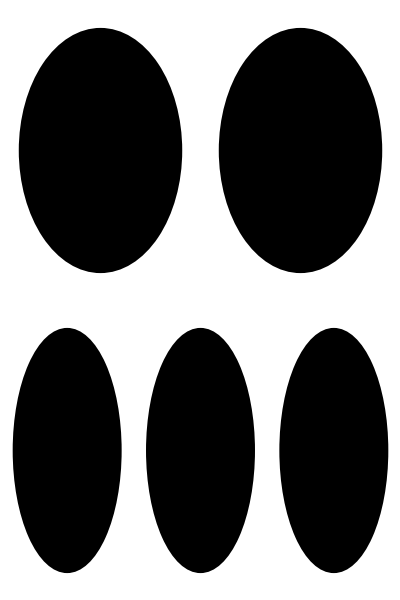

```mathematica
Pictogram[{1,2,3}]
```

Pictogram[association, opts] returns a pictogram in which the keys of the association become the labels for the rows.

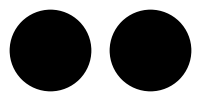
A | -Graphics-
B | -Graphics-

```mathematica
Pictogram[<|"A"->{1},"B"->{2}|>]
```

Having values that are lists of more than one number will create rows with multiple distinct objects whose styles and images can be specified.

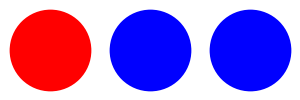
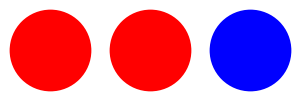
A | -Graphics-
B | -Graphics-

```mathematica
Pictogram[<|"A"->{1,2},"B"->{2,1}|>,ChartStyle->{Red,Blue}]
```

Using the ChartStyle and ChartElement options, one can specify the images/graphics and styles desired. When using graphics, ChartStyle defaults to coloring them black. With images, ChartStyle defaults to returning the original image.

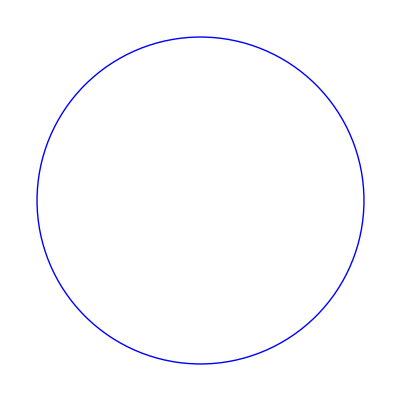
A | -Graphics-
B | -Graphics-

```mathematica
Pictogram[<|"A"->{1,2},"B"->{2,1}|>,ChartElements-> {Graphics3D[Sphere[]],Graphics[Circle[]]}, ChartStyle->{Purple,Blue}]
```

When using ChartStyle with graphics and graphics3D, it supports all graphics directives :

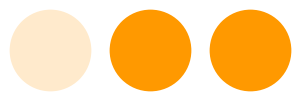
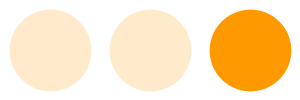
A | -Graphics-
B | -Graphics-

```mathematica
Pictogram[<|"A"->{1,2},"B"->{2,1}|>,ChartElements-> {}, ChartStyle->{Directive[Hue[0.1],Opacity[0.2]],Hue[0.1]}]
```

When using ChartStyle with images, it supports changing  Opacity by way of changing AlphaChannel and it also supports coloring functions such as Hue[], Color, etc. To apply these functions to the image, one must include them in a sublist within the ChartStyle option, beginning with the Opacity[] function if they intend to use it. Keep in mind, if an image has a white background, that will be colorized as well.

```mathematica
Pictogram[<|"A"->{1},"B"->{2}|>,ChartElements-> {-Graphics-}, ChartStyle->{{Opacity[0.7],Hue[0.1]}}]
```

A | -Graphics-
B | -Graphics-

### Other Options

One option provided to the user is to display the counts of each object to the right of the pictogram. This is the “Counts” option.

```mathematica
Pictogram[<|"A"->{1,2},"B"->{2,1}|>,ChartElements-> {}, ChartStyle->{Directive[Hue[0.1],Opacity[0.2]],Hue[0.1]},Counts->True]
```

A | -Graphics-
B | -Graphics-

Another option is to declare a title for the Pictogram, using the “Title” option.

```mathematica
Pictogram[<|"A"->{1,2},"B"->{2,1}|>,ChartElements-> {}, ChartStyle->{Directive[Hue[0.1],Opacity[0.2]],Hue[0.1]},Counts->True,Title->"Hello World"]
```

A | -Graphics-
B | -Graphics-Hello World

To specify a desired image size and display width, one can use the "ImageSize" and "DisplayWidth" options.

```mathematica
Pictogram[<|"A"->{1,2},"B"->{2,1}|>,ChartElements-> {}, ChartStyle->{Directive[Hue[0.1],Opacity[0.2]],Hue[0.1]},Counts->True,ImageSize-> 50,DisplayWidth->100]
```

A | -Graphics-
B | -Graphics-

More options include the ability to adjust spacings of the images as well as change the magnification of the images.

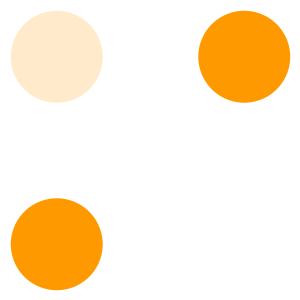
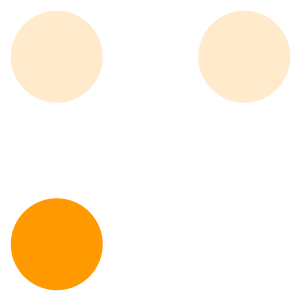
A | -Graphics-
B | -Graphics-

```mathematica
Pictogram[<|"A"->{1,2},"B"->{2,1}|>,ChartElements-> {}, ChartStyle->{Directive[Hue[0.1],Opacity[0.2]],Hue[0.1]},Counts->True,ImageSize-> 50,DisplayWidth->300,Magnification->0.25, Spacings->1]
```

When a user inputs a list of numbers as data, he or she can specify whether they want the images to be grouped together continuously or split between rows. To specify that you want them lumped together, use the “Separate->True” option. One can further specify labels for each element using the “Labels” option.

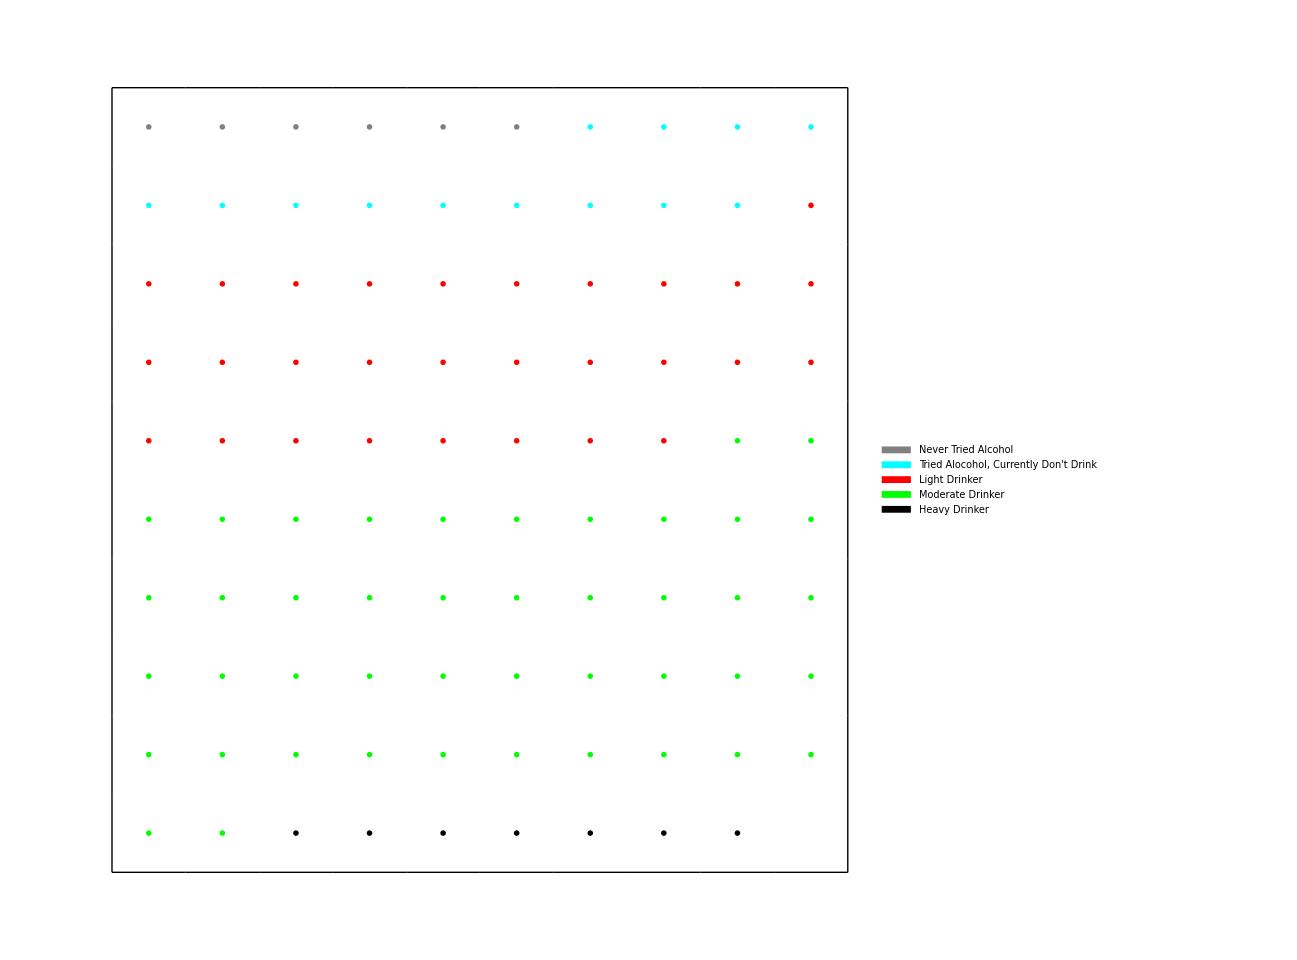
-Graphics-STUDENT SELF-REPORTED DRINKING

```mathematica
Pictogram[{6,13,29,44,7},Labels->{"Never Tried Alcohol","Tried Alocohol, Currently Don't Drink","Light Drinker","Moderate Drinker","Heavy Drinker"},Title-> Text[Style["STUDENT SELF-REPORTED DRINKING",Bold,Gray,FontSize->30]],ChartStyle->{Gray,Cyan,Red,Green,Black},Separate->False,ChartStyle->{Red,Green},Magnification->0.5,DisplayWidth->1000,Spacings-> 0.1,ImageSize->80,Frame->True,Counts->False]
```

### Other Examples


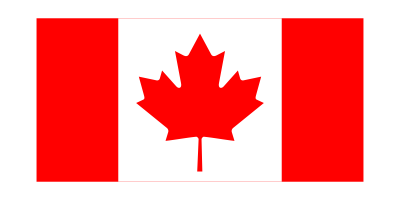


```mathematica
assoc1=Association[{-Graphics-->{5,5},-Graphics-->{3,7},-Graphics-->{2,8},-Graphics-->{5,5}}];
Pictogram[assoc1,ChartElements->{-Graphics-,-Graphics-},ChartStyle->{{},{Opacity[0.3]}},Title-> Text[Style["Number of Countries Visited by Average Citizen",Brown,FontSize->30]],Magnification->0.75,DisplayWidth->1000,Spacings-> 0.1,ImageSize->75,Frame->True,Counts->False,Magnification->0.3]
```

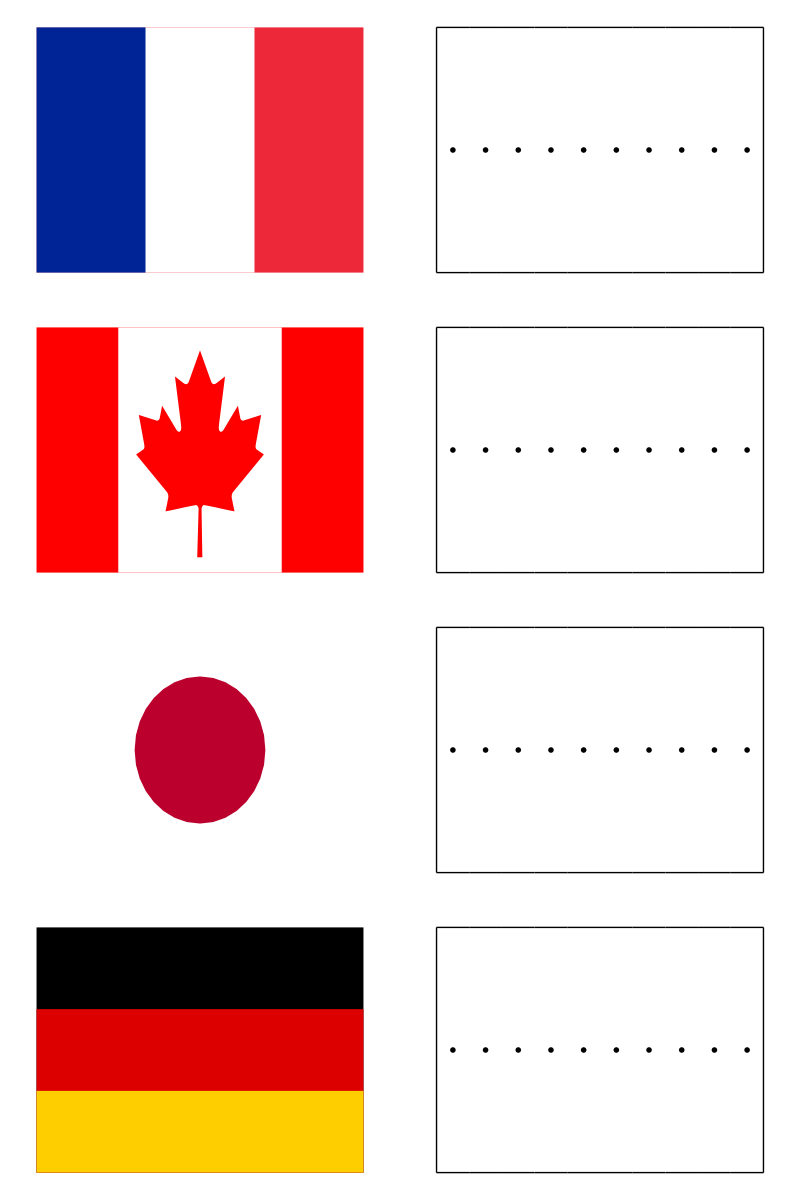
-Graphics-Number of Countries Visited by Average Citizen

## Code

### Helper Functions

#### Distribute Function

This function automatically determines the length of a given row based on the sizes of the images, the spacings, and the display width.

```mathematica
distribute[width_, numberOfItems_, imageSpacing_, displayWidth_] := 
	Module[ {lengthOfRows, numberRows, table, row},
		lengthOfRows = Floor[displayWidth/(width + 2 * imageSpacing * width)];
		numberRows = Ceiling[numberOfItems/(lengthOfRows)];
		{lengthOfRows, numberRows}
	];
```

#### Style Image Function

This function takes in an image and a list of functions to perform, such as Opacity[], Hue[], or even just a color. Currently, if the user wants to style an image, they must input a list of such functions/colors, with Opacity[] coming first in the list, if they choose to use it.

```mathematica
styleImage[img_Image, funcs_List]:=
	Module[{styledImage, opacity, colorFunctions, functions},
		If[Length[funcs] == 0,
			styledImage = img,
			If[
				ToString@Head[First[funcs]] == "Opacity" && Length[funcs] > 1, 
				colorFunctions = Take[funcs, -(Length[funcs] - 1)];
				styledImage = SetAlphaChannel[Fold[Blend[{#1,#2}]&, img, colorFunctions], 
				First[funcs]/.Opacity[x_Real] :> x]
			];
			If[
				ToString@Head[First[funcs]] == "Opacity" && Length[funcs] == 1,
				styledImage = SetAlphaChannel[img, First[funcs]/.Opacity[x_Real] :> x];
			];
			If[
				ToString@Head[First[funcs]] ≠ "Opacity",
				colorFunctions = funcs;
				styledImage = Fold[Blend[{#1, #2}]&, img, colorFunctions]
			];
		];
	styledImage
	];
```

#### Style Elements Function

This function styles all the inputted elements. For graphics/graphics3D, it simply inserts the graphic into a Style function, displaying it as a “Graphics” or “Graphics3D.” For images, this function offloads them to the styleImage[] function. The default style for graphics is applying the color black to the graphic. The default style for images is simply returning the original image.

```mathematica
styleElements[elements_List, styles_List]:=
	Module[{styledElements},
		If[
			Length[elements]≤ Length[styles],
			styledElements = 
				Table[
					If[
						ToString@Head@elements[[part]]=="Image", 
						styleImage[elements[[part]], styles[[part]]],
						If[
							styles[[part]]===None,elements[[part]],
							Style[elements[[part]],styles[[part]],
								If[
									ToString@Head[elements[[part]]] == "Graphics3D", "Graphics3D","Graphics"
								]
							]
						]
					] ,{part, Length[elements]}
				],
			If[
				Length[styles]==1,
				styledElements = 
					Table[
						If[
							ToString@Head[elements[[part]]]=="Image", 
							styleImage[elements[[part]],styles[[1]]],
							If[
								styles[[1]]===None,
								elements[[part]],
								Style[elements[[part]], styles[[1]], 
									If[
										ToString@Head[elements[[part]]] == "Graphics3D", "Graphics3D","Graphics"
									]
								]
							]
					],{part, Length[elements]}],
				Throw["Inadequate Number of Elements"]]
		];
		styledElements
	];
```

#### Remaining Function

This function is called when creating a grid of images in the Pict[] function. This function’s main objective is to generate the final row of images in a given grid.

```mathematica
remaining[numbers_,tot_,elements_]:=
	Module[{missing,lastRow},
		missing = 
				Table[
					If[
						tot-Total[Take[numbers,part - 1]]≥Part[numbers,part],
						0,
						If[
							tot-Total[Take[numbers,part - 1]]<Part[numbers,part]&&tot-Total[Take[numbers,part - 1]]>0,
							Part[numbers,part]-(tot-Total[Take[numbers,part - 1]]),
								If[
									tot-Total[Take[numbers,part - 1]]<Part[numbers,part]&&tot-Total[Take[numbers,part - 1]]≤0,
									Part[numbers,part]
								]
						]
					],{part,Length[numbers]}
				];
		lastRow = 
			Flatten[
				DeleteCases[
					Table[
						elements[[#]],{n,Part[missing,#]}
					]&/@Range[Length[numbers]],{}
				]
			]
	];
```

#### Pict Function

This function is the major function of the pictogram code. It calls styleElements[] to style the input elements, then calls distribute[] to determine the distribution of elements. It then generates a table of graphics that is displayed.

```mathematica
Pict[numbers_List, opts:OptionsPattern[{ChartElements->{Graphics[Disk[]]}, ChartStyle->{Black}, Labels->{}, Separate->False,ImageSize->100, DisplayWidth->1000, Spacings->0,Frame->True, Counts->False,Title->Nothing,Magnification->1,TableHeadings->None}]] :=
	Module[ {
		total,mag = OptionValue[Magnification], table, title, legendQ = OptionValue[Counts], 
		displayWidth = OptionValue[DisplayWidth], max, size = OptionValue[ImageSize],
		elements = OptionValue[ChartElements], resizedElements, styles = OptionValue[ChartStyle], 
		styledElementsList, lengthRows, numberRows, missing, width, styledElements, partitionedStyledElementsList,
		numberNeeded, lastRow, finalList, resizedElementsGraphics, spacing = OptionValue[Spacings],
		frameQ = OptionValue[Frame], sizeGrid, graphs, defaultElements, defaultStyles},
		total = Total[numbers];
		If[
			Length[elements] < Length[numbers], 
			defaultElements = Table[Graphics[Disk[]],{part,Length[numbers]-Length[elements]}];
			elements = Join[elements, defaultElements];
		];
		If[
			Length[styles] < Length[numbers], 
			defaultStyles=Table[Directive[Black],{part,Length[numbers]-Length[styles]}];
			styles = Join[styles, defaultStyles];
		];
		resizedElements = elements/.{im_Image:>ImageResize[im, size], im_Graphics|im_Graphics3D:>Show[im,ImageSize->size]};
		styledElements = styleElements[resizedElements,styles]/.im_Image:>Graphics[Inset[im, Automatic, Automatic,Scaled[1]]];
		styledElements = styledElements/.{Style[(Graphics[x___]),y__,z_]:>Graphics[{y,x}],Style[(Graphics3D[x___]),y__,z_]:>Graphics3D[{y,x}]};
		styledElements = styledElements/.Style[x___]:>x;
		width = ImageDimensions[resizedElements[[1]]][[1]];
		styledElementsList = Flatten[Table[Table[styledElements[[part]],numbers[[part]]],{part,Length[numbers]}]];
		lengthRows = distribute[width, total, spacing, displayWidth][[1]];
		numberRows = distribute[width, total, spacing, displayWidth][[2]];
		If[
			lengthRows > total,
			finalList = styledElementsList;
			lengthRows = Length[styledElementsList],
			partitionedStyledElementsList = Partition[styledElementsList,lengthRows];
			missing = remaining[numbers, lengthRows * (numberRows - 1), styledElements];
			If[
				total-Length[Flatten[partitionedStyledElementsList]]≠0,
				finalList = AppendTo[partitionedStyledElementsList,missing],
				finalList = partitionedStyledElementsList
			]
		];
		sizeGrid = (2 * width * spacing + width) * lengthRows;
		If[
			legendQ==True,
			If[
				numberRows == 1,
				Legended[Magnify[GraphicsRow[Flatten@finalList, ImagePadding->0,ImageSize->sizeGrid, Spacings->{Scaled[spacing],Scaled[spacing]}, Frame->frameQ],mag], SwatchLegend[Table[Black,Length[numbers]],numbers,LegendMarkers->styledElements,LegendFunction->"Frame"]],
				Legended[Magnify[GraphicsGrid[finalList, ImageSize->sizeGrid, ImagePadding->0, Spacings->Scaled[spacing], Frame->frameQ],mag],SwatchLegend[Table[Black,Length[numbers]],numbers,LegendMarkers->styledElements,LegendFunction->"Frame"]]
			],
			If[
				numberRows == 1,
				Magnify[GraphicsRow[Flatten@finalList, ImageSize->sizeGrid, ImagePadding->0, Spacings->{Scaled[spacing],Scaled[spacing]}, Frame->frameQ], mag],
				Magnify[GraphicsGrid[finalList, ImageSize->sizeGrid, ImagePadding->0, Spacings->Scaled[spacing], Frame->frameQ], mag]
			]
		]
	];
```

### Main Function

#### Pictogram Function

This function is the one that takes in the user input and determines how to proceed. It is overloaded, so it can accept an association or a list of numbers.

```mathematica
Options[Pictogram] = {
	ChartElements -> {Graphics[Disk[]]}, ChartStyle -> {Black}, ImageSize -> 100,
	DisplayWidth -> 1000, Spacings -> 0, Frame -> True, Counts -> False,
	Title -> Nothing, Magnification->1, Method->None,TableHeadings->None, Separate->True, Labels->{}};

Pictogram[assoc_Association,opts:OptionsPattern[]] :=
	Module[ {
		headers = Keys[assoc], numbs = Values[assoc], table,
		title = OptionValue[Title],
		elements = OptionValue[ChartElements]/.{{im_Image,{w_,h_}}:>ImageResize[im,{w,h}],{im_Graphics|im_Graphics3D,{w_,h_}}:>Show[im,ImageSize->{w,h}]},
		styles = OptionValue[ChartStyle], styledElements, accumulation},
		If[OptionValue[Title]==Nothing, title = ""];
		accumulation = Labeled[TableForm[Table[Pict[numbs[[part]], opts],{part, Length[numbs]}],TableHeadings->{headers,{}}],title,Top]
	];


Pictogram[numbers_List, opts:OptionsPattern[]] :=
	Module[ {
		label = OptionValue[Labels],
		size = OptionValue[ImageSize],
		styles = OptionValue[ChartStyle],
		separate = OptionValue[Separate],
		headers = OptionValue[TableHeadings],
		numbs= numbers, table,
		title = OptionValue[Title],
		elements = OptionValue[ChartElements],
		accumulation, resizedElements,styledElements,defaultElements,defaultStyles},
		
		If[
			Length[elements] < Length[numbers], 
			defaultElements = Table[Graphics[Disk[]],{part,Length[numbers]-Length[elements]}];
			elements = Join[elements, defaultElements];
		];
		If[
			Length[styles] < Length[numbers], 
			defaultStyles = Table[Directive[Black],{part,Length[numbers]-Length[styles]}];
			styles = Join[styles, defaultStyles];
		];
		
		resizedElements = elements/.{im_Image:>ImageResize[im, size], im_Graphics|im_Graphics3D:>Show[im,ImageSize->size]};
		styledElements = styleElements[resizedElements,styles]/.im_Image:>Graphics[Inset[im, Automatic, Automatic,Scaled[1]]];
		styledElements = styledElements/.{Style[(Graphics[x___]),y__,z_]:>Graphics[{y,x}],Style[(Graphics3D[x___]),y__,z_]:>Graphics3D[{y,x}]};
		styledElements = styledElements/.Style[x___]:>x;
		
		If[OptionValue[Title]==Nothing, title = ""];
		
		If[
			separate == False, 
			accumulation = Legended[Labeled[Pict[numbs,opts], title, Top],SwatchLegend[Table[Black,Length[numbers]],label,LegendMarkers->styledElements,LegendFunction->"Frame"]],
			accumulation = Labeled[TableForm[Table[Pict[{numbs[[part]]},opts],{part, Length[numbs]}],TableHeadings->{headers,{}}],title,Top]
		]

	];
```

### Future Work

Supporting the use of Wolfram Language' s new entity type, Icons.

Utilizing a classifier function to interpret input strings and display appropriate image

Distributing the images not just in a grid pattern,but on another object/shape